```mathematica
E11 = 140*10^9;E22 = 13*10^9; 
ν= 0.3; G12 = 6.6*10^9; t = 0.149*10^-3;
α11 = -8*10^-7 ; α22 = 2.9*10^-5 ;
ΔT= 120;
```

```mathematica
β = E22/E11; E0 = E11/(1-ν^2*β); γ = G12/E0;
k = 1/(1 + 2*β + β^2-4*β^2*ν^2);
k1 = 1 + 14*β + β^2-16*ν^2;
```

```mathematica
Amat=E0*t*{{1+β,2*ν*β,0},{2*ν*β,1+β,0},{0,0,2*γ}};
Bmat=0.5*E0*t^2*{{-1+β,0,0},{0,-β+1,0},{0,0,0}};
Dmat=(E0/3)*t^3*{{1+β,2*ν*β,0},{2*ν*β,1+β,0},{0,0,2*γ}};
Astar=Inverse[Amat];
Bstar=-Inverse[Amat].Bmat;
Dstar=Dmat-Transpose[Bmat].Inverse[Amat].Bmat;
```

```mathematica
Astar0={{((1+β)*k)/(E0*t),(-2*β*ν*k)/(E0*t),0},{(-2*β*ν*k)/(E0*t),((1+β)*k)/(E0*t),0},{0,0,1/(2*E0*γ*t)}};
Bstar0={{-0.5*t*k*(β^2-1),-t*β*ν*k*(β-1),0},{t*β*ν*k*(β-1),0.5*t*k*(β^2-1),0},{0,0,0}};
(*Dstar0={{(E0*t^3/12)*k*β*(β-1)*(1-β*ν^2),8*E0*t^3*k*β^2*ν*(1-β*ν^2),0},{8*E0*t^3*k*β^2*ν*(1-β*ν^2),4*E0*t^3*k*β*(β-1)*(1-β*ν^2),0},{0,0,2*E0*t^3*γ}};*)
Dstar0={{ (E0*t^3/12)*k*(1+β)*(1+14* β+β^2-16*ν^2*β^2),(E0*t^3/6)*k*β*ν*(1+14* β+β^2-16*ν^2*β^2),0},{(E0*t^3/6)*k*β*ν*(1+14* β+β^2-16*ν^2*β^2),(E0*t^3/12)*k*(1+β)*(1+14* β+β^2-16*ν^2*β^2),0},{0,0,(2/3)*E0*t^3*γ}};
```

```mathematica
Nvec={{Nx[x,y]},{Ny[x,y]},{Nxy[x,y]}}
```

{{Nx[x,y]},{Ny[x,y]},{Nxy[x,y]}}

```mathematica
AstN=Astar0.Nvecf
```

{{4.36122×10^-8,-2.22337×10^-9,0},{-2.22337×10^-9,4.36122×10^-8,0},{0,0,5.0844×10^-7}}.Nvecf

```mathematica
ϕ= s*(a^2*y^4)/(4 b^2)+s*(b^2*x^4)/(4 a^2)+s*(x^2*y^2)/2-s*(a^2*y^2)/2-s*(b^2*x^2)/2
```

-1/2 b^2 s x^2+(b^2 s x^4)/(4 a^2)-1/2 a^2 s y^2+1/2 s x^2 y^2+(a^2 s y^4)/(4 b^2)

```mathematica
ssol=Solve[k*(1+β)*D[ϕ,{x,4}]+((1/(2*γ))-4*k*β*ν)*D[D[ϕ,{x,2}],{y,2}]+k*(1+β)*D[ϕ,{y,4}]==E0*t*g,s]
```

{{s→(2.10358×10^7 g)/(21.2038+(5.5045 a^2)/b^2+(5.5045 b^2)/a^2)}}

```mathematica
ψ0=(a^2 b^2*γ)/(a^2 b^2+6 a^4 k γ+6 b^4 k γ+6 a^4 k β γ+6 b^4 k β γ-8 a^2 b^2 k β γ ν) //FullSimplify
```

(0.181669 a^2 b^2)/(1. a^4+3.85208 a^2 b^2+1. b^4)

```mathematica
s0=E0*g*t*ψ0
```

(3.82156×10^6 a^2 b^2 g)/(1. a^4+3.85208 a^2 b^2+1. b^4)

```mathematica
Nx=s*(x^2+(3 a^2*y^2)/b^2-a^2);
Ny=s*(y^2+(3 b^2*x^2)/a^2-b^2);
Nxy=-2*s*x*y;
```

```mathematica
Nvec={{Nx},{Ny},{Nxy}}/.{s->s0}
```

{{(3.82156×10^6 a^2 b^2 g (-a^2+x^2+(3 a^2 y^2)/b^2))/(1. a^4+3.85208 a^2 b^2+1. b^4)},{(3.82156×10^6 a^2 b^2 g (-b^2+(3 b^2 x^2)/a^2+y^2))/(1. a^4+3.85208 a^2 b^2+1. b^4)},{-(7.64312×10^6 a^2 b^2 g x y)/(1. a^4+3.85208 a^2 b^2+1. b^4)}}

```mathematica
Nxxth=E0*ΔT*t*(α11+β*α22+ν*β*(α11+α22));
Nyyth=Nxxth;
Nxyth=0;
Mxxth=-0.5*E0*ΔT*t^2*(-α11+β*α22+ν*β*(α11-α22));
Myyth=-Mxxth;
Mxyth=0;
```

```mathematica
kvec={{kxx},{kyy},{2*kxy}};
Nthvec={{Nxxth},{Nyyth},{Nxyth}};
Mthvec={{Mxxth},{Myyth},{Mxyth}};
```

```mathematica
U=0.5*Transpose[Nvec].Astar0.Nvec + 0.5*Transpose[kvec].Dstar0.kvec-0.5*Transpose[Nthvec].Astar0.Nthvec-Transpose[Nthvec].Bstar0.kvec-Transpose[Mthvec].kvec/. {ψ-> ψ0 ,s-> s0, g-> kxx*kyy-kxy*kxy}/.{k ->  1/(1 + 2*β + β^2-4*β^2*ν^2),g-> kxx*kyy-kxy*kxy, a-> η, b-> 1}//Expand// Rationalize//Simplify
```

{{1/((1.+3.85208 η^2+η^4)^2)(-1.89201-0.102923 kyy+0.0409919 kyy^2-14.5764 η^2-0.792937 kyy η^2+0.315808 kyy^2 η^2-31.8587 η^4-1.73308 kyy η^4+0.690244 kyy^2 η^4-14.5764 η^6-0.792937 kyy η^6+0.315808 kyy^2 η^6-1.89201 η^8-0.102923 kyy η^8+0.0409919 kyy^2 η^8+kxy^2 (0.02911+0.224268 η^2+0.490169 η^4+0.224268 η^6+0.02911 η^8)+kxy^4 (x^4 (2.86617×10^6-97412.4 η^2+318464. η^4)+x^2 η^2 (-1.91078×10^6+129883. η^2-636927. η^4+y^2 (1.91078×10^6+1.45262×10^7 η^2+1.91078×10^6 η^4))+η^4 (318464.-32470.8 η^2+318464. η^4+y^2 (-636927.+129883. η^2-1.91078×10^6 η^4)+y^4 (318464.-97412.4 η^2+2.86617×10^6 η^4)))+kxx^2 (0.0409919+0.315808 η^2+0.690244 η^4+0.315808 η^6+0.0409919 η^8+kyy^2 (x^4 (2.86617×10^6-97412.4 η^2+318464. η^4)+x^2 η^2 (-1.91078×10^6+129883. η^2-636927. η^4+y^2 (1.91078×10^6+1.45262×10^7 η^2+1.91078×10^6 η^4))+η^4 (318464.-32470.8 η^2+318464. η^4+y^2 (-636927.+129883. η^2-1.91078×10^6 η^4)+y^4 (318464.-97412.4 η^2+2.86617×10^6 η^4))))+kxx (0.102923+0.792937 η^2+1.73308 η^4+0.792937 η^6+0.102923 η^8+kyy (0.00417957+0.0322001 η^2+0.0703778 η^4+0.0322001 η^6+0.00417957 η^8+kxy^2 (x^4 (-5.73234×10^6+194825. η^2-636927. η^4)+x^2 η^2 (3.82156×10^6-259766. η^2+1.27385×10^6 η^4+y^2 (-3.82156×10^6-2.90523×10^7 η^2-3.82156×10^6 η^4))+η^4 (-636927.+64941.6 η^2-636927. η^4+y^4 (-636927.+194825. η^2-5.73234×10^6 η^4)+y^2 (1.27385×10^6-259766. η^2+3.82156×10^6 η^4))))))}}

```mathematica
Utot=Integrate[U,{x,y}∈Disk[{0,0},{η,1}]]//Rationalize//Expand//Simplify
```

{{ConditionalExpression[1/((1.+3.85208 η^2+η^4)^2)η (-5.94393-0.323343 kyy+0.12878 kyy^2-45.793 η^2-2.49109 kyy η^2+0.992142 kyy^2 η^2-100.087 η^4-5.44462 kyy η^4+2.16847 kyy^2 η^4-45.793 η^6-2.49109 kyy η^6+0.992142 kyy^2 η^6-5.94393 η^8-0.323343 kyy η^8+0.12878 kyy^2 η^8+kxy^2 (0.0914516+0.704559 η^2+1.53991 η^4+0.704559 η^6+0.0914516 η^8)+kxy^4 (500241. η^4+1.92697×10^6 η^6+500241. η^8)+kxx^2 (0.12878+0.992142 η^2+(2.16847+500241. kyy^2) η^4+(0.992142+1.92697×10^6 kyy^2) η^6+(0.12878+500241. kyy^2) η^8)+kxx (0.323343+2.49109 η^2+5.44462 η^4+2.49109 η^6+0.323343 η^8+kyy (0.0131305+0.10116 η^2+(0.221099-1.00048×10^6 kxy^2) η^4+(0.10116-3.85394×10^6 kxy^2) η^6+(0.0131305-1.00048×10^6 kxy^2) η^8))),η>0]}}

```mathematica
eq1=D[Utot,kxx];
eq2=D[Utot,kyy];
eq3=D[Utot,kxy];
```

```mathematica
soln=NSolve[{eq1[[1,1,1]]==0 &&eq2[[1,1,1]]==0&&eq3[[1,1,1]]==0},{kxx,kyy,kxy},Reals]
```

{{kxx→ConditionalExpression[(0.-2.98455×10^74 η-2.29935×10^75 η^3-5.02555×10^75 η^5-2.29935×10^75 η^7-2.98455×10^74 η^9-1.21198×10^73 η ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-9.33733×10^73 η^3 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-2.04081×10^74 η^5 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-9.33733×10^73 η^7 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-1.21198×10^73 η^9 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2))))/(2.37735×10^74 η+1.83155×10^75 η^3+4.00312×10^75 η^5+1.83155×10^75 η^7+2.37735×10^74 η^9+9.23476×10^80 η^5 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))^2+3.55731×10^81 η^7 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))^2+9.23476×10^80 η^9 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))^2),η>0.0288094||η<-0.0288094],kyy→ConditionalExpression[(0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)-1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)),η>0.0288094||η<-0.0288094],kxy→ConditionalExpression[0,η>0.0288094||η<-0.0288094]},{kxx→ConditionalExpression[(0.-2.98455×10^74 η-2.29935×10^75 η^3-5.02555×10^75 η^5-2.29935×10^75 η^7-2.98455×10^74 η^9-1.21198×10^73 η ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-9.33733×10^73 η^3 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-2.04081×10^74 η^5 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-9.33733×10^73 η^7 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))-1.21198×10^73 η^9 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2))))/(2.37735×10^74 η+1.83155×10^75 η^3+4.00312×10^75 η^5+1.83155×10^75 η^7+2.37735×10^74 η^9+9.23476×10^80 η^5 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))^2+3.55731×10^81 η^7 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))^2+9.23476×10^80 η^9 ((0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)))^2),η>0.0288094||η<-0.0288094],kyy→ConditionalExpression[(0.0128501 (1.8381×10^22+1.4161×10^23 η^2+3.09509×10^23 η^4+1.4161×10^23 η^6+1.8381×10^22 η^8))/(3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)+1.0455×10^-44 √((-6.7037×10^137-1.54939×10^139 η^2+9.76098×10^143 η^4+1.88022×10^145 η^6+1.4974×10^146 η^8+6.33225×10^146 η^10+1.51911×10^147 η^12+2.05687×10^147 η^14+1.51911×10^147 η^16+6.3323×10^146 η^18+1.49743×10^146 η^20+1.8803×10^145 η^22+9.76251×10^143 η^24)/(η^4 (1.91275×10^15+7.36806×10^15 η^2+1.91275×10^15 η^4) (3.76288×10^20+2.89899×10^21 η^2+6.33615×10^21 η^4+2.89899×10^21 η^6+3.76288×10^20 η^8)^2)),η>0.0288094||η<-0.0288094],kxy→ConditionalExpression[0,η>0.0288094||η<-0.0288094]},{kxx→ConditionalExpression[(0.-2.98455×10^74 η-2.29935×10^75 η^3-5.02555×10^75 η^5-2.29935×10^75 η^7-2.98455×10^74 η^9-1.21198×10^73 η Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-9.33733×10^73 η^3 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-2.04081×10^74 η^5 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-9.33733×10^73 η^7 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-1.21198×10^73 η^9 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1])/(2.37735×10^74 η+1.83155×10^75 η^3+4.00312×10^75 η^5+1.83155×10^75 η^7+2.37735×10^74 η^9+9.23476×10^80 η^5 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2+3.55731×10^81 η^7 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2+9.23476×10^80 η^9 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2),-0.0288094<η<0.0288094||η>0.0288094||η<-0.0288094],kyy→ConditionalExpression[Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1],-0.0288094<η<0.0288094||η>0.0288094||η<-0.0288094],kxy→ConditionalExpression[0,-0.0288094<η<0.0288094||η>0.0288094||η<-0.0288094]}}

```mathematica
soln[[1,1,2]]/.{η-> 1.5}
```

-1.25541

```mathematica
eq3[[1,1,1]]
```

(η (2 kxy (0.0914516+0.704559 η^2+1.53991 η^4+0.704559 η^6+0.0914516 η^8)+4 kxy^3 (500241. η^4+1.92697×10^6 η^6+500241. η^8)+kxx kyy (-2.00097×10^6 kxy η^4-7.70789×10^6 kxy η^6-2.00097×10^6 kxy η^8)))/((1.+3.85208 η^2+η^4)^2)

```mathematica
D[Utot,kxy]
```

{{ConditionalExpression[(η (2 kxy (0.0914516+0.704559 η^2+1.53991 η^4+0.704559 η^6+0.0914516 η^8)+4 kxy^3 (500241. η^4+1.92697×10^6 η^6+500241. η^8)+kxx kyy (-2.00097×10^6 kxy η^4-7.70789×10^6 kxy η^6-2.00097×10^6 kxy η^8)))/((1.+3.85208 η^2+η^4)^2),η>0]}}

```mathematica
eq1
```

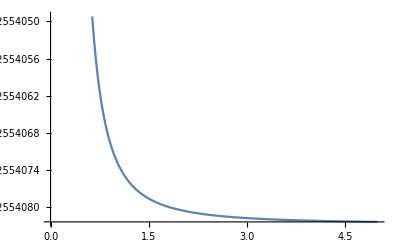

```mathematica
s1x=Plot[soln[[1,1,2]],{η,0,5}]
```

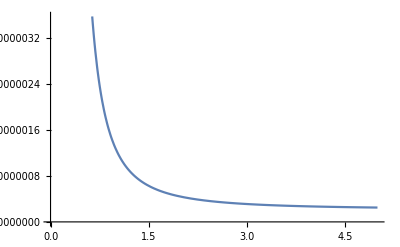

```mathematica
s1y=Plot[soln[[1,2,2]],{η,0,5}]
```

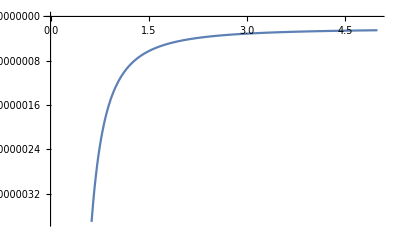

```mathematica
s2x=Plot[soln[[2,1,2]],{η,0,5}]
```

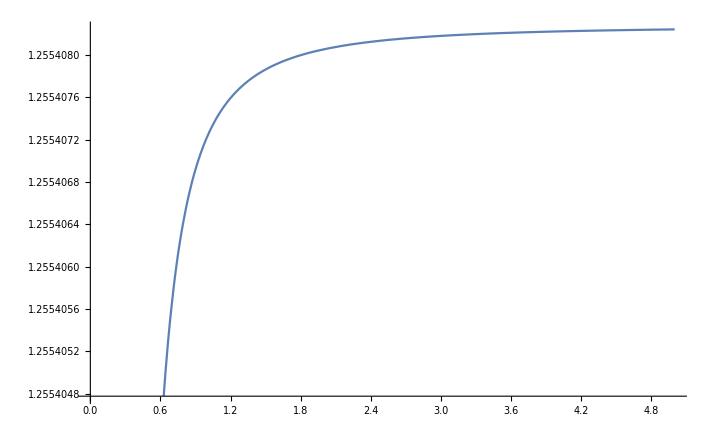

```mathematica
s2y=Plot[soln[[2,2,2]],{η,0,5}]
```

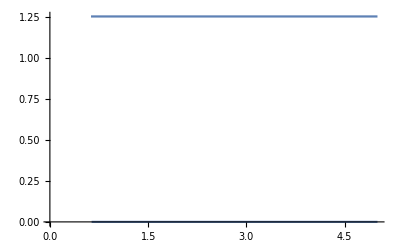

```mathematica
Show[s1y,s2y,PlotRange-> {{0.01,5},{0, 1.2554 }}]
```

```mathematica
Show[s1y,s2y,PlotRange-> {{0.62,0.63},{1.2554, 1.25547}}]
```

```mathematica
w1 = 0.5*(kxx*x^2 + kyy*y^2) + kxy*x*y/.soln[[3]]
```

ConditionalExpression[0.5 (y^2 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]+(x^2 (0.-2.98455×10^74 η-2.29935×10^75 η^3-5.02555×10^75 η^5-2.29935×10^75 η^7-2.98455×10^74 η^9-1.21198×10^73 η Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-9.33733×10^73 η^3 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-2.04081×10^74 η^5 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-9.33733×10^73 η^7 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]-1.21198×10^73 η^9 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]))/(2.37735×10^74 η+1.83155×10^75 η^3+4.00312×10^75 η^5+1.83155×10^75 η^7+2.37735×10^74 η^9+9.23476×10^80 η^5 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2+3.55731×10^81 η^7 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2+9.23476×10^80 η^9 Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2)),-0.0288094<η<0.0288094||η>0.0288094||η<-0.0288094]

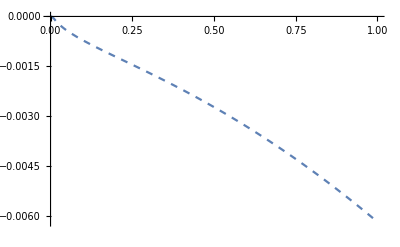

```mathematica
p3=Plot[0.5*(kxx*x^2 + kyy*y^2) + kxy*x*y/.soln[[3]]/. {x-> η, y-> 0}, {η,0,1},PlotRange->All, PlotStyle->Dashed]
```

```mathematica
w1
```

```mathematica
wfunc2=0.5 (y^2 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))+(x^2 (0.-2.9845508981044104*^74 η-2.2993483287452663*^75 η^3-5.025551973149688*^75 η^5-2.2993483287452663*^75 η^7-2.9845508981044104*^74 η^9-1.2119845982296555*^73 η ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))-9.337333674471216*^73 η^3 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))-2.040806740112427*^74 η^5 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))-9.337333674471216*^73 η^7 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))-1.2119845982296555*^73 η^9 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))))/(2.377354404219709*^74 η+1.8315539130693544*^75 η^3+4.003120913297453*^75 η^5+1.8315539130693544*^75 η^7+2.377354404219709*^74 η^9+9.234760991928996*^80 η^5 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))^2+3.5573077789761107*^81 η^7 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))^2+9.234760991928996*^80 η^9 ((0.012850123849149495 (1.8380974593988471*^22+1.416101271391956*^23 η^2+3.095090226067287*^23 η^4+1.416101271391956*^23 η^6+1.8380974593988471*^22 η^8))/(3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)+1.0454992338449939*^-44 √((-6.703698483045182*^137-1.5493926989007458*^139 η^2+9.760982803405098*^143 η^4+1.8802171767930778*^145 η^6+1.4974003877900234*^146 η^8+6.332252996131962*^146 η^10+1.519108105748393*^147 η^12+2.05687006006136*^147 η^14+1.5191128118043184*^147 η^16+6.332303212934291*^146 η^18+1.4974270649899925*^146 η^20+1.8803000101849756*^145 η^22+9.762508419718265*^143 η^24)/(η^4 (1.912746698840026*^15+7.368061519882611*^15 η^2+1.912746698840026*^15 η^4) (3.762883591334328*^20+2.8989889575992385*^21 η^2+6.336151636473534*^21 η^4+2.8989889575992385*^21 η^6+3.762883591334328*^20 η^8)^2)))^2));
```

```mathematica
wfunc3=0.5 (y^2 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]+(x^2 (0.-2.9845508981044104*^74 η-2.2993483287452663*^75 η^3-5.025551973149688*^75 η^5-2.2993483287452663*^75 η^7-2.9845508981044104*^74 η^9-1.2119845982296555*^73 η Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]-9.337333674471216*^73 η^3 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]-2.040806740112427*^74 η^5 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]-9.337333674471216*^73 η^7 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]-1.2119845982296555*^73 η^9 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]))/(2.377354404219709*^74 η+1.8315539130693544*^75 η^3+4.003120913297453*^75 η^5+1.8315539130693544*^75 η^7+2.377354404219709*^74 η^9+9.234760991928996*^80 η^5 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]^2+3.5573077789761107*^81 η^7 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]^2+9.234760991928996*^80 η^9 Root[-2.9845508981044104*^74-2.2993483287452663*^75 η^2-5.025551973149688*^75 η^4-2.2993483287452663*^75 η^6-2.9845508981044104*^74 η^8+(2.2561559443967435*^74+1.7381805763246422*^75 η^2+3.7990402392862104*^75 η^4+1.7381805763246422*^75 η^6+2.2561559443967435*^74 η^8) #1+(9.234760991928996*^80 η^4+3.5573077789761107*^81 η^6+9.234760991928996*^80 η^8) #1^3&,1]^2));
```

```mathematica
wfunca0 =wfunc/.{x-> η, y-> 0}//Simplify;
wfunc2a0 = wfunc2/.{x-> η, y-> 0}//Simplify;
wfunc3a0 = wfunc3/.{x-> η, y-> 0}//Simplify;
```

```mathematica
wfunca0/.{x-> η, y-> 0, η-> 0.0288094413677441}
```

-0.000260492

```mathematica
wfunc2a0/.{x-> η, y-> 0, η-> 0.0288094413677441}
```

-0.000260492

```mathematica
wfunca0/.{x-> η, y-> 0, η-> 0.05}
```

-0.00152446

```mathematica
wfunc2a0/.{x-> η, y-> 0, η-> 0.05}
```

-0.0000447972

```mathematica
wfunc3a0/.{x-> η, y-> 0}
```

```mathematica
wfunc3a0
```

(0.5 η^2 (-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(-1.21198×10^73-9.33733×10^73 η^2-2.04081×10^74 η^4-9.33733×10^73 η^6-1.21198×10^73 η^8) Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]))/(2.37735×10^74+1.83155×10^75 η^2+4.00312×10^75 η^4+1.83155×10^75 η^6+2.37735×10^74 η^8+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) Root[-2.98455×10^74-2.29935×10^75 η^2-5.02555×10^75 η^4-2.29935×10^75 η^6-2.98455×10^74 η^8+(2.25616×10^74+1.73818×10^75 η^2+3.79904×10^75 η^4+1.73818×10^75 η^6+2.25616×10^74 η^8) #1+(9.23476×10^80 η^4+3.55731×10^81 η^6+9.23476×10^80 η^8) #1^3&,1]^2)

```mathematica
p3 = Plot[wfunc3a0,{η,0.01,0.1},PlotRange->All]
```

-Graphics-

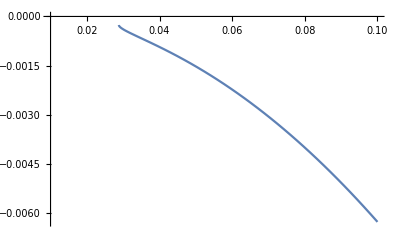

```mathematica
p1=Plot[wfunca0,{η,0.01,0.1}]
```

```mathematica
wfunc2a0
```

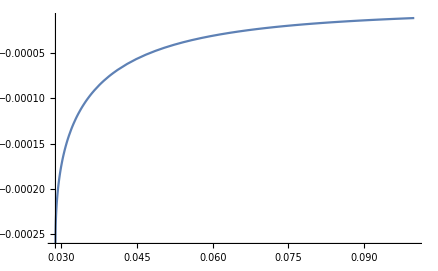

```mathematica
p2=Plot[wfunc2a0,{η,0.01,0.1},PlotRange->All]
```

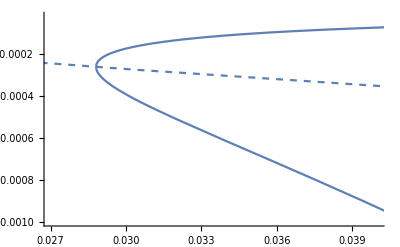

```mathematica
Show[p1,p2,p3, PlotRange-> {{.027,0.04},{- 0.001, -0.00002}}]
```

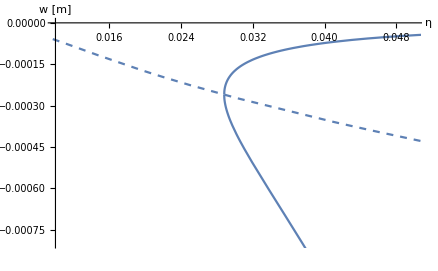

```mathematica
Show[p1,p2,p3, PlotRange-> {{ 0.01,0.05},{- 0.0008,0}},Axes-> {True,True},AxesLabel->{"η","w [m]"}]
```

```mathematica
Export["plot-eta-bifur.pdf",%228,"PDF","AllowRasterization"->False]
```

plot-eta-bifur.pdf

```mathematica
SystemOpen["plot-eta-bifur.pdf"]
```

```mathematica
File@Directory[]
```

File[C:\Users\ayanhaldar\Documents]

```mathematica
wfunc2a0/.{x-> η, y-> 0, η-> 0.03}
```

-0.00017332

```mathematica
Plot3D[wfunca0,{a,-8,8},{η,-8,8}]
```

-Graphics3D-